## Аналитическая часть

```mathematica
mat = {{-A, 0, c1^2/τ+ A}, {0, -B, c2^2/τ+ B}, {A, B, -(c1^2/τ + A+c2^2/τ+ B)}};
ME = MatrixExp[mat t];
IC = {1/2, 1/2, 0};
```

```mathematica
σ13[δν_, v_,sign_]:= c1^2 1/(1 + ((δν + sign*a*v)/(Γ/2))^2);
σ23[δν_, v_,sign_]:= c2^2 1/(1 + ((δν + sign*a*v)/(Γ/2))^2);
subA = σ13[δν, v,-1]s; (* на самом деле ~3.5s *)

subB = σ23[δν + Δ, v,-1]s;
subAB = {A-> subA, B-> subB};

{EQ1, EQ2, EQ3} = (ME/. {t-> Ν τ}).IC(*/. {A-> subA, B -> subB}*) ;
β13 = EQ1-EQ3;
β23 = EQ2-EQ3;
```

```mathematica
sub  = {Γ -> 6, a -> 3/2, c1 -> 2^(-1/2), c2 ->2^(-1/2), τ-> 27 10^-3, Ν -> 30, Δ-> 228, s-> 4 25};
subΝ  = {Γ -> 6, a -> 3/2, c1 -> 2^(-1/2), c2 ->2^(-1/2), τ-> 27 10^-3, Δ-> 228, s-> 100};
subS  = {Γ -> 6, a -> 3/2, c1 -> 2^(-1/2), c2 ->2^(-1/2), τ-> 27 10^-3, Ν -> 100, Δ-> 228};
ClearAll[GetNumsΝ,GetNumsS, GetNums];
GetNums[eq_] :=(eq  /. subAB )/. sub;
GetNumsΝ[eq_, Νv_] :=((eq  /. subAB )/. subΝ)/. {Ν-> Νv};
GetNumsS[eq_, sv_] :=((eq  /. subAB )/. subS) /. {s-> sv};
```

## Интегрирование

```mathematica
ClearAll[GetHValS];
σV = 20;
GetHValS[sv_, ν_:0] := NIntegrate[GetNumsS[EQ2, 4 sv] 1/(√(2 π σV^2))Exp[-v^2/(2 σV^2)] /. {δν-> ν}, {v, -100, 100}] ;
```

```mathematica
X = Join[Range[0.01,100, 1]]; 
Print["time: ", Length[X]/20./4]
AbsoluteTiming[Y = ParallelMap[GetHValS, X];]
Y = Y-1/2;
data = {X, Y}ᵀ;
```

time: 2.5

{6.71928,Null}

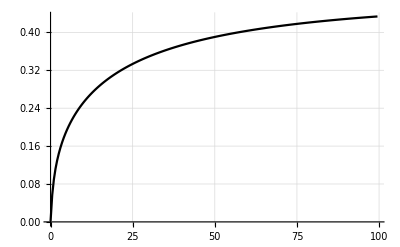

```mathematica
Show[{
ListLinePlot[data, PlotStyle->Black, PlotRange->Full, GridLines->Automatic]
(*,ListPlot[{2.2Xexp,1.8 Yexp}ᵀ, PlotStyle->Red]*)
}]
```